# Imbalance-Induced Energy Loss

A draft of my work  “Analytical Estimation for Imbalance-Induced Energy Loss” 
Han Wu, Hohai University, China
E-mail: wuhan@hhu.edu.cn 
Working on this project During <16th Mar 2020, 18th Mar 2020 >
Copyrights reserved

```mathematica
directory = "D:\\OneDrive - 河海大学\\Data"; (* change to where you place the data *)
datafile = FileNameJoin[{directory, "WPD_load.wl"}];
ReadList[datafile]; (*data name: threephasedata*)
```

```mathematica
Ia = threephasedata[[All,1]];
Ib = threephasedata[[All,2]];
Ic = threephasedata[[All,3]];
r = 0.1;
Δt = 60*10;
```

```mathematica
μa = Mean[Ia];μb = Mean[Ib];μc = Mean[Ic];
σa = Variance[Ia];σb = Variance[Ib];σc = Variance[Ic];
COVab = Covariance[threephasedata][[1,2]];COVac = Covariance[threephasedata][[1,3]];COVbc = Covariance[threephasedata][[2,3]];
```

```mathematica
EstIprc2 = σa+σb+σc -COVab-COVac-COVbc+μa^2+μb^2+μc^2-μa*μb-μb*μc-μa*μc;
EstEnergyLoss = EstIprc2*Δt*r*Length[Ia]/(3600*1000);
Print["The estimated energy loss is ",EstEnergyLoss," kWh"]
```

The estimated energy loss is 2085.92 kWh

## Define the Phase Residual Current

Let Ia, Ib, Ic be the phase current supported by each phase, Iprc denotes the phase residual current. Suppose the resistance and reactance of three-phase are the same, that is, the phase angles of three-phases are fixed as 120 degree.

```mathematica
Iprc2=Ia^2+Ib^2+Ic^2-Ia*Ib-Ia*Ic-Ib*Ic;
NeutralEnergyLoss = Total[Iprc2*r*Δt/(3600*1000)];

Print["The true energy loss on neutral line is ",NeutralEnergyLoss," kWh"]
```

The actual Neutral Energy Loss is ： 2085.85 kWh

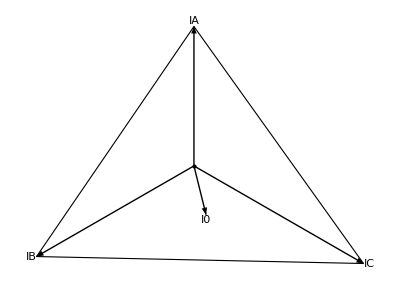

```mathematica
Module[{r,θ,IA,IB,IC,I0},
r = {10,13,14};
θ = {90 Degree,90Degree+120Degree,90Degree+120Degree+120 Degree};
IA = AngleVector[{r[[1]],θ[[1]]}];
IB = AngleVector[{r[[2]],θ[[2]]}];
IC = AngleVector[{r[[3]],θ[[3]]}];
I0 = IA+IB+IC;
Graphics[{
Black,Point[{0,0}],(* 向量图原点 *)
Arrow[{{0,0},IA}],Arrow[{{0,0},IB}],Arrow[{{0,0},IC}],(* 三相电流向量 *)
Inset["IA",IA,Bottom],Inset["IB",IB,Right],Inset["IC",IC,Left],(* 相电流标注 *)
FaceForm[],EdgeForm[Dashing[Medium]],Triangle[{IA,IB,IC}],(* 三角形虚线外框 *)
(*Red,Point[RegionCentroid[Triangle[{IA,IB,IC}]]](* 三角形几何中心，红色点 *),*)
(*Blue,TriangleConstruct[Triangle[{IA,IB,IC}],"Orthocenter"](* 三角形重中心，红色点 *),*)
Black,Arrow[{{0,0},I0}],Inset["I0",I0,Top](* 中性点电流/不平衡电流 *)},
Background-> None]]
```

## Methodology

The phase residual current is a linear combination of products of correlated variables. 
Iprc2=Ia^2+Ib^2+Ic^2-Ia*Ib-Ia*Ic-Ib*Ic;
Since the phase current is written as a mixture of normal variables, the product term can also derived.

### Bayesian method to build distribution from small number of observations

```mathematica
λ𝒟=MatrixPropertyDistribution[RandomSample[Eigenvalues[x]],x\[Distributed]InverseWishartMatrixDistribution[10,{{1,1/3},{1/3,1}}]];
SmoothHistogram3D[RandomVariate[λ𝒟,10^4],PlotRange->{{-.1,.5},{-.1,.5},Automatic}]
```

-Graphics3D-

When new data are obtained from field measurement, the NIW distribution parameters: µ0, k0, λ0, and v0 should be upgraded as,
μ_0*=(κ_0 μ_0+n x^(.af))/(κ_0+n)
k_0*=k_0+n
v_0*=v_0+n
λ_0*=λ_0+∑_(i=1)^n (x_i−μ)(x_i−μ)^T+(k_0 n)/(k_0+n)(x^(.af)−μ_0)(x^(.af)−μ_0)^T 
where xi denotes the new measurements;  denotes the statistical mean of the new measurements; n denotes the number of the new measurements; µ0*, v0*, k0* and λ0* are the upgraded parameters of NIW distribution. 
Machine Learning A Probabilistic Perspective P.134

```mathematica
(*sampleing from original data*)
SeedRandom[2](*SeedRandom[2]*)
samplestart = Table[RandomInteger[{1+(i-1)*Length[Ia]/10,i*Length[Ia]/10},1],{i,1,10}]//Flatten;
samples = Table[threephasedata[[Range[samplestart[[i]],samplestart[[i]]+9],All]],{i,1,10}];

(*get the coveriance*)
covs = Map[Covariance, samples];
(*fit InverseWishartMatrixDistribution and normal distribution*)
edist𝒲 = EstimatedDistribution[covs[[Range[1,2]]],InverseWishartMatrixDistribution[n, Array[a, {3, 3}]]];
edist𝒩 = EstimatedDistribution[Flatten[samples,1],MultinormalDistribution[Array[n,3], Array[a, {3, 3}]]];

(*GET the initial parameter*)
Subscript[λ, 0] = DiagonalMatrix[Diagonal[Covariance[samples[[1,All]]]]]/Length[samples[[1,All]]]; 
Subscript[v, 0] = 5; (*D+2*)
Subscript[μ, 0] = Mean[samples[[1,All]]];
Subscript[k, 0] = 0.01; 

Print["μ_0 = ",Subscript[μ, 0]//MatrixForm]
Print["k_0 = ",Subscript[k, 0]//MatrixForm]
Print["λ_0 = ",Subscript[λ, 0]//MatrixForm]
Print["v_0 = ",Subscript[v, 0]//MatrixForm]
```

μ_0 = (77.4277
129.067
148.25)

k_0 = 0.01

λ_0 = (1.19085 | 0. | 0.
0. | 5.92312 | 0.
0. | 0. | 1.95493)

v_0 = 5

```mathematica
SuperStar[μ][i_] := Which[i==1,(Subscript[k, 0]*Subscript[μ, 0]+Length[samples[[i+1]]]*Mean[samples[[i+1]]])/(Subscript[k, 0]+Length[samples[[i+1]]]),
				1<i≤9,(SuperStar[k][i-1]*SuperStar[μ][i-1]+Length[samples[[i+1]]]*Mean[samples[[i+1]]])/(SuperStar[k][i-1]+Length[samples[[i+1]]])];
SuperStar[k][i_] := Which[i==1,Subscript[k, 0]+Length[samples[[i+1]]],1<i≤9,SuperStar[k][i-1]+Length[samples[[i+1]]]];
SuperStar[v][i_] := Which[i==1,Subscript[v, 0]+Length[samples[[i+1]]],1<i≤9,SuperStar[v][i-1]+Length[samples[[i+1]]]];
SuperStar[λ][i_] := Which[i==1,Block[{ave,n,y},
					ave = Mean[samples[[i+1]]];
					n = Length[samples[[i+1]]];
					y = samples[[i+1]];
					(*prior+empirical scatter matrix+the uncertainty in the mean*)
					Subscript[λ, 0]+Sum[KroneckerProduct[y[[j]]-ave,y[[j]]-ave],{j,1,n}] +(Subscript[k, 0]*n)/(Subscript[k, 0]+n)*KroneckerProduct[ave-Subscript[μ, 0],ave-Subscript[μ, 0]]],
				1<i≤9,Block[{ave,n,y},
					ave = Mean[samples[[i+1]]];
					n = Length[samples[[i+1]]];
					y = samples[[i+1]];
					SuperStar[λ][i-1]+Sum[KroneckerProduct[y[[j]]-ave,y[[j]]-ave],{j,1,n}]+(SuperStar[k][i-1]*n)/(SuperStar[k][i-1]+n)*KroneckerProduct[ave-SuperStar[μ][i-1],ave-SuperStar[μ][i-1]]]];
```

argmax p(μ,Σ|D)=(μ^*, λ^*/(v^*+D+2))

```mathematica
totalityMean = Mean[threephasedata];
totalityCov  = Covariance[threephasedata];

sampleMean = edist𝒩[[1]];
sampleCov  = edist𝒩[[2]];

BayesianMean = SuperStar[μ][9];
BayesianCov = (SuperStar[λ][9])/(SuperStar[v][9]+3+2);

Print["totalityMean = ",totalityMean//MatrixForm]
Print["totalityCov = ",Sqrt[totalityCov]//MatrixForm]

Print["sampleMean（frequentist point of view） = ",sampleMean//MatrixForm]
Print["sampleCov（frequentist point of view）= ",Sqrt[sampleCov]//MatrixForm]

Print["sampleMean（Bayesian point of view） = ",BayesianMean//MatrixForm]
Print["sampleCov（Bayesian point of view）= ",Sqrt[BayesianCov]//MatrixForm]
```

totalityMean = (187.046
262.922
229.56)

totalityCov = (74.162 | 73.9159 | 54.0648
73.9159 | 87.6346 | 58.533
54.0648 | 58.533 | 54.6394)

sampleMean（frequentist point of view） = (166.036
238.855
204.968)

sampleCov（frequentist point of view）= (77.5865 | 79.5086 | 51.1689
79.5086 | 95.9756 | 53.6373
51.1689 | 53.6373 | 45.8981)

sampleMean（Bayesian point of view） = (175.871
251.04
211.263)

sampleCov（Bayesian point of view）= (71.7438 | 72.4138 | 45.3928
72.4138 | 88.7032 | 46.7443
45.3928 | 46.7443 | 41.8073)

#### Moment Matching Through Gamma Distribution

```mathematica
totalityMean = Mean[threephasedata];
totalityCov  = Covariance[threephasedata];

A = {{1,-0.5,-0.5},{-0.5,1,-0.5},{-0.5,-0.5,1}};
μneutral = (Tr[A.totalityCov]+totalityMean.A.totalityMean)*r*Δt*Length[Ia]/(3600*1000)
Σneutral = (2*Tr[A.totalityCov]^2+4*totalityMean.A.totalityCov.A.totalityMean)*(r*Δt*Length[Ia]/(3600*1000))^2
skeneutral = (8*(Tr[A.totalityCov]^3+3*totalityMean.((A.totalityCov)^2).A.totalityMean)+6*(Tr[A.totalityCov]^2+2*totalityMean.A.totalityCov.totalityMean)*(Tr[A.totalityCov]+totalityMean.A.totalityMean)+(Tr[A.totalityCov]+totalityMean.A.totalityMean)^3)*(r*Δt*Length[Ia]/(3600*1000))^3
```

2085.92

3.80567×10^6

1.26964×10^11

```mathematica
gdist = GammaDistribution[a,b];
moments = Through[{Mean, Variance}[gdist]]; 
nmoments = {μneutral,Σneutral};
sol = Solve[Thread[moments == nmoments], {a,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→1.14331,b→1824.46}}

```mathematica
MonteCarlo = (Ia^2+Ib^2+Ic^2-Ia*Ib-Ib*Ic-Ia*Ic)*Δt*r*Length[Ia]/(3600*1000);
```

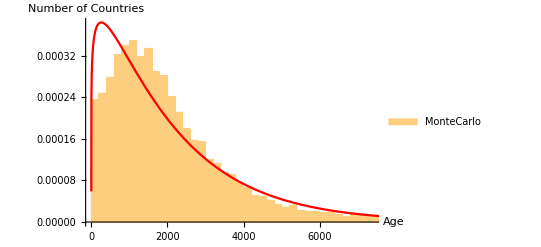

```mathematica
Show[Histogram[MonteCarlo,100,"PDF",ChartLegends->{"MonteCarlo"},AxesLabel->{"Current(A)","PDF"}],
Plot[PDF[gdist,x]/.sol,{x,0,10000},PlotStyle->Red,PlotLegends->"Expressions"]]
```